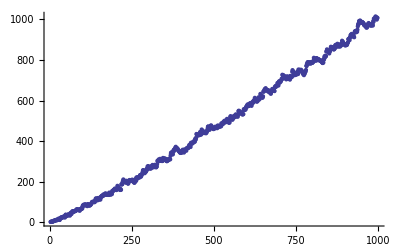

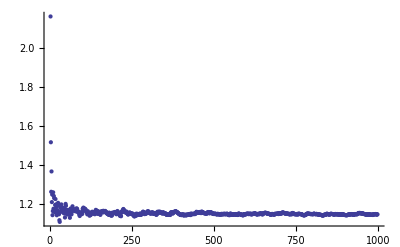

```mathematica
A={};B={};(*定义空集*)
For[i=2,i<1000,i++,A=A∪{{i,Prime[i](*第i个素数*)-i Log[i]}};B=B∪{{i,Prime[i]/(i Log[i])}}];(*A是以(n,第n个素数与n ln n的差)为点的二维散点图*)
ListPlot[A]
ListPlot[B]
```